## Quantenoptik 2

### 1. Vorlesung

#### 3-level system, Eigenstates

```mathematica
({{0, Ωp, 0}, {Ωp, -2Δp, Ωs}, {0, Ωs, 2(0)}})
Eigenvectors[%]
```

{{0,Ωp,0},{Ωp,-2 Δp,Ωs},{0,Ωs,0}}

{{-Ωs/Ωp,0,1},{Ωp/Ωs,-(Δp+√(Δp^2+Ωp^2+Ωs^2))/Ωs,1},{Ωp/Ωs,-(Δp-√(Δp^2+Ωp^2+Ωs^2))/Ωs,1}}

#### EIT

```mathematica
Imχ=(8δ^2 γ2+2γ3(Ωc^2+γ2 γ3))/((4Δp δ-γ3 γ2-Ωc^2)^2+4(γ3 δ +γ3 Δp)^2)
Reχ=(-4δ(Ωc^2-4δ Δp)+4Δp γ3^2)/((4Δp δ-γ3 γ2-Ωc^2)^2+4(γ3 δ +γ3 Δp)^2)
```

(8 γ2 δ^2+2 γ3 (γ2 γ3+Ωc^2))/(4 (γ3 δ+γ3 Δp)^2+(-γ2 γ3+4 δ Δp-Ωc^2)^2)

(4 γ3^2 Δp-4 δ (-4 δ Δp+Ωc^2))/(4 (γ3 δ+γ3 Δp)^2+(-γ2 γ3+4 δ Δp-Ωc^2)^2)

```mathematica
Imχ=(8δ^2 γ2+2γ3(Ωc^2+γ2 γ3))/(Abs[Ωc^2+(γ2+I 2Δp)(γ3+I 2δ)]^2)
Reχ=(4δ(Ωc^2-4δ Δp)-4Δp γ3^2)/(Abs[Ωc^2+(γ2+I 2Δp)(γ3+I 2δ)]^2)
```

(8 γ2 δ^2+2 γ3 (γ2 γ3+Ωc^2))/(Abs[(γ3+2 ⅈ δ) (γ2+2 ⅈ Δp)+Ωc^2]^2)

(-4 γ3^2 Δp+4 δ (-4 δ Δp+Ωc^2))/(Abs[(γ3+2 ⅈ δ) (γ2+2 ⅈ Δp)+Ωc^2]^2)

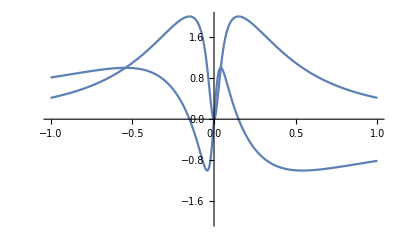

```mathematica
Plot[{Imχ,Reχ}/.{δ->Δp,γ2->1,γ3->0,Ωc->0.3},{Δp,-1,1},PlotRange->{-2,2}]
```

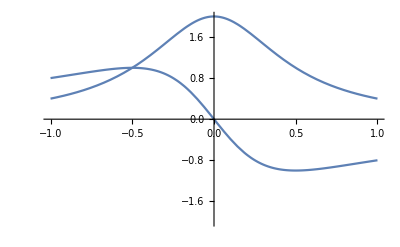

```mathematica
Plot[{Imχ,Reχ}/.{δ->Δp,γ2->1,γ3->0,Ωc->0},{Δp,-1,1},PlotRange->{-2,2}]
```

#### Slow light

```mathematica
re=Reχ/.{γ3->0}
im=Imχ/.{γ3->0}
```

(4 δ (-4 δ Δp+Ωc^2))/(Abs[2 ⅈ δ (γ2+2 ⅈ Δp)+Ωc^2]^2)

(8 γ2 δ^2)/(Abs[2 ⅈ δ (γ2+2 ⅈ Δp)+Ωc^2]^2)

```mathematica
re=Simplify[ComplexExpand[re=Reχ/.{γ3->0}],Assumptions->{δ>0,γ2>0,Δp>0,Ωc>0}]
re=Simplify[re/.δ->Δp]
```

(4 δ (-4 δ Δp+Ωc^2))/(4 γ2^2 δ^2+(-4 δ Δp+Ωc^2)^2)

(4 Δp (-4 Δp^2+Ωc^2))/(4 γ2^2 Δp^2+(-4 Δp^2+Ωc^2)^2)

```mathematica
Denominator[re]
```

4 γ2^2 Δp^2+(-4 Δp^2+Ωc^2)^2

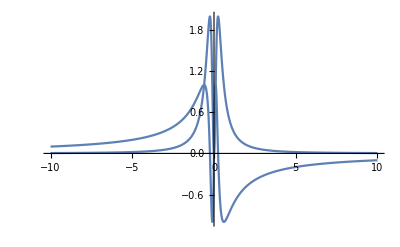

```mathematica
Plot[{re,im}/.{Ωc->0.5,γ2->1},{Δp,-10,10},PlotRange->All]
```

```mathematica
n=1+1/2 re
```

1+(2 Δp (-4 Δp^2+Ωc^2))/(4 γ2^2 Δp^2+(-4 Δp^2+Ωc^2)^2)

```mathematica
n=Simplify[Re[ComplexExpand[n]],Assumptions->{Δp>0,Ωc>0,γ2>0}]
```

```mathematica
1+(-8 Δp^3 iiii8kkkkkkkkkkkk+2 Δp Ωc^2)/(4 γ2^2 Δp^2+(-4 Δp^2+Ωc^2)^2)
```

```mathematica
Simplify[ D[n,Δp]]
%/.Δp->0
n/.Δp->0
```

(2 (4 Δp^2+Ωc^2) (-4 γ2^2 Δp^2+(-4 Δp^2+Ωc^2)^2))/((4 γ2^2 Δp^2+(-4 Δp^2+Ωc^2)^2)^2)

2/Ωc^2

1

```mathematica
re/.{Δp->0}
D[re,Δp]/.{Δp->0}
```

0

4/Ωc^2

```mathematica
v=1/Simplify[(re/.δ->Δp)+Δp Simplify[D[(re/.δ->Δp),Δp]]]
```

-((4 γ2^2 Δp^2+(-4 Δp^2+Ωc^2)^2)^2)/(8 Δp (16 γ2^2 Δp^4-(-4 Δp^2 Ωc+Ωc^3)^2))

```mathematica
vs=v/.{γ2->1}
```

-((4 Δp^2+(-4 Δp^2+Ωc^2)^2)^2)/(8 Δp (16 Δp^4-(-4 Δp^2 Ωc+Ωc^3)^2))

```mathematica
Plot[v/.{ψ2->1,Δp->0}]
```

Plot[v/.{ψ2→1,Δp→0}]